```mathematica
SetDirectory[NotebookDirectory[]];
vChoices={{2,4},{3,1},{4,2},{1,3}};
lSize={2,1,6,2};
fSelect[aNumber_Integer,lChoices__]:=Module[{aNext=RandomInteger[{1,2}]},lChoices[[aNumber,aNext]]]
fSelectAndMove[aNumber_Integer,lChoices__,lWts__]:=Module[{aNext=fSelect[aNumber,lChoices],p=RandomReal[],r},r=lWts[[aNext]]/lWts[[aNumber]]; If[p<r,aNext,aNumber]]
```

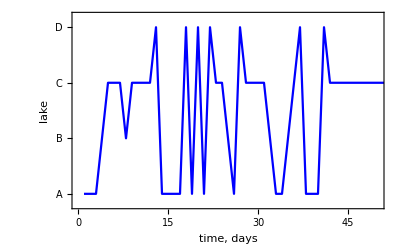

```mathematica
n=50;
lSeq=NestList[fSelectAndMove[#,vChoices,lSize]&,1,n];
lTime=Range@(n+1);
yTicks={{1,"A"},{2,"B"},{3,"C"},{4,"D"}};
xTicks=Table[{-10i,10i},{i,1,10,1}];
aFish=Import["fish.pdf"];
g1=Show[GraphicsRow[{ListLinePlot[Thread[{lTime,lSeq}],PlotRange->{{0,n},{0.8,4.2}},Frame->{True,True,False,False},PlotStyle->Blue,FrameTicks->{True,yTicks},FrameLabel->{"time, days","lake"},BaseStyle->{FontSize->Medium}],BarChart[Sort[Tally[lSeq]][[All,2]],BarOrigin->Right,ChartElements->aFish,BarSpacing->1,Frame->{True,False,False,True},FrameTicks->{xTicks,yTicks},FrameLabel->{"lake","fish caught"},BaseStyle->{FontSize->Medium}]}],ImageSize->800]
```

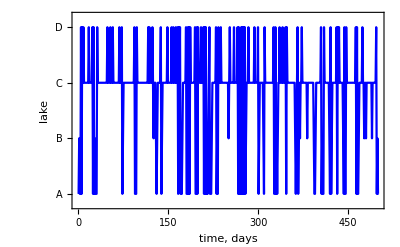

```mathematica
n=500;
lSeq=NestList[fSelectAndMove[#,vChoices,lSize]&,1,n];
lTime=Range@(n+1);
yTicks={{1,"A"},{2,"B"},{3,"C"},{4,"D"}};
xTicks=Table[{-100i,100i},{i,1,10,1}];
aFish=Import["fish.pdf"];
g2=Show[GraphicsRow[{ListLinePlot[Thread[{lTime,lSeq}],PlotRange->{{0,n},{0.8,4.2}},Frame->{True,True,False,False},PlotStyle->Blue,FrameTicks->{True,yTicks},FrameLabel->{"time, days","lake"},BaseStyle->{FontSize->Medium}],BarChart[Sort[Tally[lSeq]][[All,2]],BarOrigin->Right,ChartElements->aFish,BarSpacing->1,Frame->{True,False,False,True},FrameTicks->{xTicks,yTicks},FrameLabel->{"lake","fish caught"},BaseStyle->{FontSize->Medium}]}],ImageSize->800]
```

```mathematica
gFinal=Show[GraphicsColumn[{g1,g2}],ImageSize->800];
```

```mathematica
Export["metropolisHastings_metropolisFish.pdf",gFinal]
```

metropolisHastings_metropolisFish.pdf

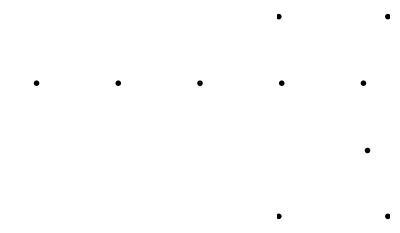

```mathematica
gOther=BarChart[lSize,BarOrigin->Right,BarOrigin->Right,ChartElements->aFish,BarSpacing->1,Frame->{True,False,False,True},FrameTicks->{xTicks,yTicks},FrameLabel->{"lake","total fish"},BaseStyle->{FontSize->Medium}]
```

```mathematica
Export["metropolisHastings_totalfish.pdf",gOther]
```

metropolisHastings_totalfish.pdf